## Нечеткое множество, нечеткое число

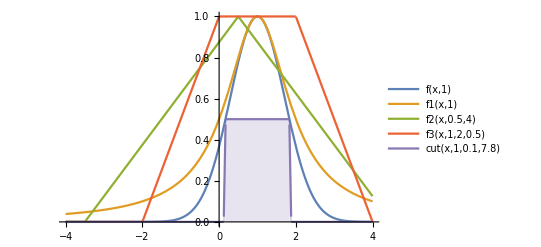

```mathematica
(* Одномерное нечеткое множество *)
f[x_, a_]:=Exp[-(x-a)^2];
f1[x_,a_]:=1/(1+Abs[x-a]^2);
f2[x_,a_,b_]:=Max[(b-Abs[x-a])/b,0];
f3[x_,a_,b_, c_]:=Min[1,Max[0,c+(b-Abs[x-a])/b]];
cut[x_,a_,b_, c_]:=Min[0.5,Max[0,c+(b-Abs[x-a])/b]];
Plot[
{
f[x,1], 
f1[x,1], 
f2[x,0.5,4], 
f3[x,1,2,0.5],
cut[x,1,0.1, 7.8]
},
{x,-4,4}, 
PlotLegends->"Expressions",
Filling->{5->Axis}]
```

```mathematica
(* Двумерное нечеткое множество *)
f2d[x_,y_,a_,b_]:=Exp[-((x-a)^2+(y-b)^2)];
Plot3D[
f2d[x,y,1,0],
{x,-4,4}, 
{y,-4,4},
PlotLegends->"Expressions",
Filling->{1->Axis},
PlotRange->All]
```

-Graphics3D-

### Операции над нечеткими множествами

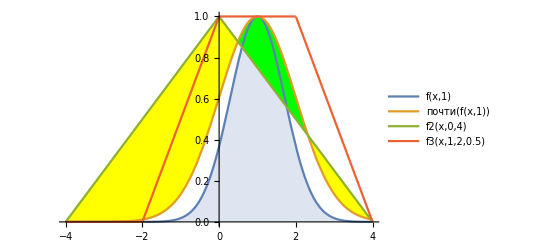

```mathematica
очень[x_]:=x^2;
почти[x_]:=Sqrt[x];
Plot[
{
f[x,1],
почти[f[x,1]],
f2[x,0,4], 
f3[x,1,2,0.5]
},
{x,-4,4}, 
PlotLegends->"Expressions",
Filling->{2->{{3},{Yellow, Green}},1->Axis}]
```

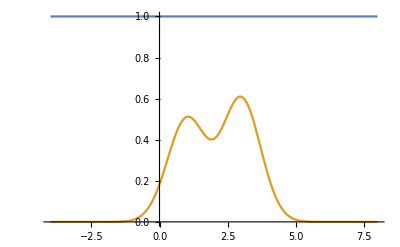

```mathematica
(* Поднормальное не выпуклое нечеткое множество *)
Plot[{1,(f[x,1]+1.2*f[x,3])/2},{x,-4,8}]
```

```mathematica
(* Дискретное нечеткое множество *)
a={1.2->0.1,2->0.8,3.4->0.7,2.7->0.9,2.4->0.2,2.5->0.22};
ListPlot[a]
```

-Graphics-

Треугольная норма

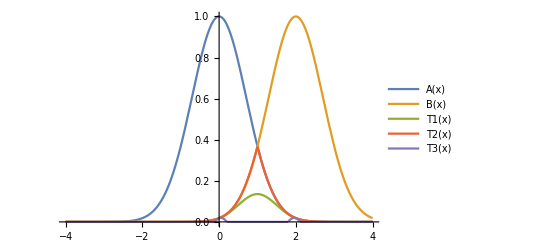

```mathematica
A[x_]:=f[x,0];
B[x_]:=f[x,2];
T1[t_]:=A[t]*B[t];
T2[t_]:=Min[A[t],B[t]];
T3[t_]:=Max[0,A[t]+B[t]-1];
Plot[{A[x],B[x],T1[x],T2[x], T3[x]},{x,-4,4}, PlotRange->Full,PlotLegends->"Expressions"]
```

## Треугольная конорма

```mathematica
S1[t_]:=Max[A[t],B[t]];
S2[t_]:=Min[A[t]+B[t],1];
S3[t_]:=A[t]+B[t]-A[t]*B[t];
```

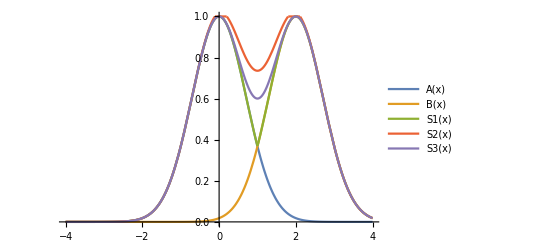

```mathematica
Plot[{A[x],B[x],S1[x],S2[x], S3[x]},{x,-4,4}, PlotRange->Full,PlotLegends->"Expressions"]
```

## Нечеткое отношение

```mathematica
R1[x_,y_]:=Exp[-(x^2+y^2)];
R2[x_,y_]:=Min[1,2*Exp[-((x-2)^2+y^2)]];

Plot3D[{R1[x,y],R2[x,y]},{x,-4,4},{y,-4,4},PlotRange->Full, PlotLegends->"Expressions", PlotRange->All]
```

-Graphics3D-

```mathematica
union[x_,y_]:=Max[R1[x,y],R2[x,y]]
intersection[x_,y_]:=Min[R1[x,y],R2[x,y]];
sum[x_,y_]:=R1[x,y]+R2[x,y]-R1[x,y]*R2[x,y];
product[x_,y_]:=R1[x,y]*R2[x,y];

Plot3D[union[x,y],{x,-4,4},{y,-4,4},PlotRange->Full,PlotLegends->"Expressions", PlotRange->All]
Plot3D[intersection[x,y],{x,-4,4},{y,-4,4},PlotRange->Full,PlotLegends->"Expressions", PlotRange->All]
Plot3D[sum[x,y],{x,-4,4},{y,-4,4},PlotRange->Full,PlotLegends->"Expressions", PlotRange->All]
Plot3D[product[x,y],{x,-4,4},{y,-4,4},PlotRange->Full,PlotLegends->"Expressions", PlotRange->All]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»